# Decaimiento del Higgs a dos fotones en VHDMM

```mathematica
$LoadPhi=True;
Needs["HighEnergyPhysics`FeynCalc`"];
```

Loading FeynCalc from /home/bastilo/.Mathematica/Applications/HighEnergyPhysics

HighEnergyPhysics`FeynCalc`MemoryAvailable`MemoryAvailable::shdw: Symbol MemoryAvailable appears in multiple contexts {HighEnergyPhysics`FeynCalc`MemoryAvailable`,System`}; definitions in context HighEnergyPhysics`FeynCalc`MemoryAvailable` may shadow or be shadowed by other definitions.

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading PHI

WARNING! Your FeynArts installation is not complete or the version you have cannot be used with this version of FeynCalc.
FeynArts can be downloaded at www.feynarts.de

Loading FeynArts, see www.feynarts.de for documentation

FeynArts not found. Please install FeynArts, e.g., in
/home/bastilo/.Mathematica
and reload FeynCalc
FeynArts can be downloaded from www.feynarts.de

## Definiciones

```mathematica
dm[mu_]:=DiracMatrix[mu]
dm[5]:=DiracMatrix[5]
ds[p_]:=DiracSlash[p]
mt[mu_,nu_]:=MetricTensor[mu,nu]
fv[p_,mu_]:=FourVector[p,mu]
epsilon[a_,b_,c_,d_]:=LeviCivita[a,b,c,d]
id[n_]:=IdentityMatrix[n]
sp[p_,q_]:=ScalarProduct[p,q]
li[mu_]:=LorentzIndex[mu]
prop[p_,m_]:=ds[p]+m
PR:=(1+dm[5])/2
PL:=(1-dm[5])/2
ϵA[p_,mu_]:=PolarizationVector[p,mu]
propW[p_,mu_,nu_]:=ⅈ*(-mt[mu,nu]+(fv[p,mu]*fv[p,nu])/MW^2)*FeynAmpDenominator[{p,MW}]
propf[p_,Mf_]:=ⅈ*prop[p,Mf]*FeynAmpDenominator[{p,Mf}]
propV[p_,mu_,nu_]:=I*(-mt[mu,nu]+(fv[p,mu]*fv[p,nu])/MVC^2)*FeynAmpDenominator[{p,MVC}]
```

```mathematica
Feynman Rules
```

Feynman Rules

```mathematica
(*SM*)

(*HWW*)
ΓHWW[mu_,nu_]:=ⅈ*g*MW*mt[mu,nu]
(*AWW*)
ΓAWW[p1_,p2_,p3_,mu_,nu_,rho_]:=-ⅈ*e*((-fv[p1,rho]+fv[p2,rho])*mt[mu,nu]+(-fv[p2,mu]+fv[p3,mu])*mt[nu,rho]+(-fv[p3,nu]+fv[p1,nu])*mt[mu,rho])
(*AAWW*)
ΓAAWW[mu_,nu_,rho_,sig_]:=-ⅈ*e^2*(2mt[mu,nu]*mt[rho,sig]-mt[mu,rho]*mt[nu,sig]-mt[mu,sig]*mt[nu,rho])

(*ffH*)
ΓHff[Mf_]=-ⅈ*(e*Mf)/(2MW*sw);
(*Aff*)
ΓAff[mu_,Q_]=-ⅈ*Q*e*dm[mu];

(*VHM*)

(*HVCVC*)(*ok*)
ΓHVCVC[mu_,nu_]:=-2*I*(MW*sw*λ2)/e*mt[mu,nu]
ΓAVCVC[p1_,p2_,p3_,mu_,nu_,rho_]:=ΓAWW[0,p2,p3,mu,nu,rho]
(*AVCVC*)
(*ΓAVCVC[p1_,p2_,p3_,mu_,nu_,rho_]:=-ⅈ*e*(fv[p2,rho].mt[mu,nu]+(-fv[p2,mu]+fv[p3,mu]).mt[nu,rho]+fv[p3,nu].mt[mu,rho])*)
(*AAWW*)
ΓAAVCVC[mu_,nu_,rho_,sig_]:=-ⅈ*e^2*(2mt[mu,nu].mt[rho,sig]-mt[mu,rho].mt[nu,sig]-mt[mu,sig].mt[nu,rho])
```

```mathematica
Restrictions
```

Restrictions

```mathematica
onshell={sp[k1,k1]->0,sp[k2,k2]->0,sp[k1,k2]->MH^2/2};
R=p-k1;
q=p-k1-k2;
var0={sw->e/g};
```

```mathematica
Amplitudes
```

Amplitudes

```mathematica
1.- W's;
```

```mathematica
MW1=2*Simplify[Contract[ΓHWW[alpha,alpha].propW[p,alpha,beta].ΓAWW[-k1,-R,p,mu,rho,beta].propW[R,rho,sig].ΓAWW[-k2,-q,R,nu,gamma,sig].propW[q,gamma,alpha].ϵA[k1,mu].ϵA[k2,nu]]];
MW12=Simplify[MW1/.onshell];
MW13=I/(64*π^4)*Simplify[PaVeReduce[OneLoop[p,MW12]]];
MW14=FullSimplify[MW13/.onshell];
(*MW14=Series[MW13,{sp[k1,k1],0,1},{sp[k2,k2],0,1}];*)
```

```mathematica
MW21=Simplify[Contract[ΓHWW[alpha,alpha].propW[p,alpha,beta].ΓAAWW[mu,nu,gamma,beta].ϵA[k1,mu].propW[q,gamma,alpha].ϵA[k2,nu]]]/.onshell;
MW22=I/(64*π^4)*Simplify[PaVeReduce[OneLoop[p,MW21]]];
MW24=FullSimplify[MW22/.onshell];
```

```mathematica
MTW=FullSimplify[MW14+MW24];
MTWC=Coefficient[MTW,MH^2*Contract[ϵA[k1,mu].ϵA[k2,mu]]-2*Contract[fv[k1,mu].ϵA[k2,mu]]*Contract[fv[k2,mu].ϵA[k1,mu]],1]*(MH^2 mt[mu,nu]-2Contract[mt[a,nu]fv[k1,a]mt[b,mu]fv[k2,b]]);
```

```mathematica
2.- Fermions;
```

```mathematica
Mtop=(-2)*Simplify[NC*Contract[Tr[Contract[ΓHff[Mt].propf[p,Mt].ΓAff[mu,2/3].propf[R,Mt].ΓAff[nu,2/3].propf[q,Mt]]].ϵA[k1,mu].ϵA[k2,nu]]];
Mtop=Simplify[PaVeReduce[OneLoop[p,Mtop]]];
Mtop=FullSimplify[I/(16*π^4)*Mtop/.onshell];
MtopC=Coefficient[Mtop,MH^2*Contract[ϵA[k1,mu].ϵA[k2,mu]]-2*Contract[fv[k1,mu].ϵA[k2,mu]]*Contract[fv[k2,mu].ϵA[k1,mu]],1]*(MH^2 mt[mu,nu]-2Contract[mt[a,nu]fv[k1,a]mt[b,mu]fv[k2,b]]);
```

```mathematica
Mbot=(-2)*Simplify[NC*Contract[Tr[Contract[ΓHff[Mb].propf[p,Mb].ΓAff[mu,-1/3].propf[R,Mb].ΓAff[nu,-1/3].propf[q,Mb]]].ϵA[k1,mu].ϵA[k2,nu]]];
Mbot=Simplify[PaVeReduce[OneLoop[p,Mbot]]];
Mbot=FullSimplify[I/(16*π^4)*Mbot/.onshell];
MbotC=Coefficient[Mbot,MH^2*Contract[ϵA[k1,mu].ϵA[k2,mu]]-2*Contract[fv[k1,mu].ϵA[k2,mu]]*Contract[fv[k2,mu].ϵA[k1,mu]],1]*(MH^2 mt[mu,nu]-2Contract[mt[a,nu]fv[k1,a]mt[b,mu]fv[k2,b]]);
```

```mathematica
Mcha=(-2)*NC*FullSimplify[Contract[Tr[Contract[ΓHff[Mc].propf[p,Mc].ΓAff[mu,2/3].propf[R,Mc].ΓAff[nu,2/3].propf[q,Mc]]].ϵA[k1,mu].ϵA[k2,nu]]];
Mcha=Simplify[PaVeReduce[OneLoop[p,Mcha]]];
Mcha=FullSimplify[I/(16*π^4)*Mcha/.onshell];
MchaC=Coefficient[Mcha,MH^2*Contract[ϵA[k1,mu].ϵA[k2,mu]]-2*Contract[fv[k1,mu].ϵA[k2,mu]]*Contract[fv[k2,mu].ϵA[k1,mu]],1]*(MH^2 mt[mu,nu]-2Contract[mt[a,nu]fv[k1,a]mt[b,mu]fv[k2,b]]);
```

```mathematica
Mtau=(-2)*Simplify[Contract[Tr[Contract[ΓHff[Mτ].propf[p,Mτ].ΓAff[mu,-1].propf[R,Mτ].ΓAff[nu,-1].propf[q,Mτ]]].ϵA[k1,mu].ϵA[k2,nu]]];
Mtau=Simplify[PaVeReduce[OneLoop[p,Mtau]]];
Mtau=FullSimplify[I/(16*π^4)*Mtau/.onshell];
MtauC=Coefficient[Mtau,MH^2*Contract[ϵA[k1,mu].ϵA[k2,mu]]-2*Contract[fv[k1,mu].ϵA[k2,mu]]*Contract[fv[k2,mu].ϵA[k1,mu]],1]*(MH^2 mt[mu,nu]-2Contract[mt[a,nu]fv[k1,a]mt[b,mu]fv[k2,b]]);
```

```mathematica
Introduzco el cambio de variables βw->(4 MW^2)/MH^2 y βt->(4 Mt^2)/MH^2;
```

```mathematica
var1:={C0[0,0,MH^2,MW^2,MW^2,MW^2]->-(2/MH^2)*(XW-2-3*βw)/(3*βw*(2-βw))}
var2:={C0[0,0,MH^2,Mt^2,Mt^2,Mt^2]->-(2/MH^2)*((XFt+2*βt)/(2*βt))*1/(βt-1)}
var3:={C0[0,0,MH^2,Mb^2,Mb^2,Mb^2]->-(2/MH^2)*((XFb+2*βb)/(2*βb))*1/(βb-1)}
var4:={C0[0,0,MH^2,Mc^2,Mc^2,Mc^2]->-(2/MH^2)*((XFc+2*βc)/(2*βc))*1/(βc-1)}
var5:={C0[0,0,MH^2,Mτ^2,Mτ^2,Mτ^2]->-(2/MH^2)*((XFτ+2*βτ)/(2*βτ))*1/(βτ-1)}
var6:={βw->4*MW^2/MH^2}
var7:={βt->4*Mt^2/MH^2}
var8:={βb->4*Mb^2/MH^2}
var9:={βc->4*Mc^2/MH^2}
var10:={βτ->4*Mτ^2/MH^2}
```

```mathematica
MWF=FullSimplify[MTWC/.var1/.var6];
MtF=FullSimplify[MtopC/.var0/.var2/.var7];
MbF=FullSimplify[MbotC/.var0/.var3/.var8];
McF=FullSimplify[MchaC/.var0/.var4/.var9];
Mttau=FullSimplify[MtauC/.var0/.var5/.var10];
```

```mathematica
Total amplitude
```

amplitude Total

```mathematica
MAT=FullSimplify[MWF+MtF+MbF+McF+Mttau];
MMT=Simplify[Contract[MAT.MAT]];
MMSM=FullSimplify[MMT/.onshell/.{e->√(4*π*α)}/.{g->√((8*GF*MW^2)/(√2))}];
```

```mathematica
AnchoHAA[XFt_,XFb_,XFc_,XFτ_,XW_]=(4π)/(64*π^2*MH)MMSM*(1/2)
```

(α^2 GF MH^3 (NC (XFb+4 (XFc+XFt))+9 (XFτ+XW))^2)/(10368 √2 π^3)

```mathematica
f[x_]:=Piecewise[{{(ArcSin[√(1/x)])^2,x≥1},{-1/4*(Log[(1+√(1-x))/(1-√(1-x))-ⅈ*π])^2,x<1}}]
XW[β_]:=2+3*β+3*β*(2-β)*f[β]
XF[β_]:=-2*β*(1+(1-β)*f[β])
XFt[a_]:=XF[a]
XFb[a_]:=XF[a]
XFc[a_]:=XF[a]
XFτ[a_]:=XF[a]
```

```mathematica
Re[Block[{MH=125,Mt=172.50,Mb=4.250,Mc=1.230,Mτ=1.777,MW=80.385,GF=1.2057*10^-5,NC=3,α=1/137},AnchoHAA[XFt[4*Mt^2/MH^2],XFb[4*Mb^2/MH^2],XFc[4*Mc^2/MH^2],XFτ[4*Mτ^2/MH^2],XW[4*MW^2/MH^2]]]]
```

9.64683×10^-6

```mathematica
TWH=4.07*10^-3(*GeV*)
```

0.00407

```mathematica
(9.64*10^-6)/(4.07*10^-3)
```

0.00236855

```mathematica
New Vectors amplitudes;
```

```mathematica
MV11=2*Simplify[Contract[ΓHVCVC[alpha,alpha].propV[p,alpha,beta].ΓAVCVC[-k1,-R,p,mu,rho,beta].propV[R,rho,sig].ΓAVCVC[-k2,-q,R,nu,gamma,sig].propV[q,gamma,alpha].ϵA[k1,mu].ϵA[k2,nu]]]/.onshell;
MV12=I/(64*π^4)*Simplify[PaVeReduce[OneLoop[p,MV11]]]/.onshell;
```

```mathematica
MV21=Simplify[Contract[ΓHVCVC[alpha,alpha].propV[p,alpha,beta].ΓAAVCVC[mu,nu,gamma,beta].propV[q,gamma,alpha].ϵA[k1,mu].ϵA[k2,nu]]];
MV22=FullSimplify[MV21/.onshell];
MV23=I/(64*π^4)*Simplify[PaVeReduce[OneLoop[p,MV22]]];
MV24=FullSimplify[MV23/.onshell];
```

```mathematica
simpPV={B0[0,MVC^2,MVC^2]->A0[MVC^2]/MVC^2 -1};
MVT=MV12+MV24;
MVT2=MVT/.simpPV;
```

```mathematica
MV25=FullSimplify[Coefficient[MVT2,MH^2*Contract[ϵA[k1,mu].ϵA[k2,mu]]-2*Contract[fv[k1,mu].ϵA[k2,mu]]*Contract[fv[k2,mu].ϵA[k1,mu]],1]*(MH^2 mt[mu,nu]-2Contract[mt[a,nu]fv[k1,a]mt[b,mu]fv[k2,b]])]
```

-(e λ2 MW sw B_0(0,MVC^2,MVC^2) (MH^2 g^munu-2 k_2^mu k_1^nu))/(12 π^2 MVC^2)

```mathematica
SUMA DE AMPLITUDES
```

AMPLITUDES DE SUMA

```mathematica
MF=FullSimplify[MAT+MV25]/.{A0[MVC^2]->AO}/.{B0[MH^2,MVC^2,MVC^2]->BO};
```

```mathematica
MF
```

-(e (MH^2 g^munu-2 k_2^mu k_1^nu) (24 AO λ2 MW^2 sw+e g MVC^4 (NC (XFb+4 (XFc+XFt))+9 (XFτ+XW))-24 λ2 MVC^2 MW^2 sw))/(288 π^2 MVC^4 MW)

```mathematica
MFC=ComplexConjugate[MF]
```

-(e (MH^2 g^munu-2 k_2^mu k_1^nu) (24 AO λ2 MW^2 sw+e g MVC^4 (NC (XFb+4 (XFc+XFt))+9 (XFτ+XW))-24 λ2 MVC^2 MW^2 sw))/(288 π^2 MVC^4 MW)

```mathematica
MF1=FullSimplify[Contract[MFC.MF]/.onshell/.{e->√(4*π*α)}/.{g->√((8*GF*MW^2)/(√2))}/.var0/.{λ2->λL+2*((MV1^2-MVC^2)/vv^2)}];
```

```mathematica
MF11=MF1/.{g->√((8*GF*MW^2)/(√2))}
```

1/(648 π^3 MVC^8 MW^2)α MH^4 ((3 AO e MW^2 (λL+(2 (MV1-MVC) (MV1+MVC))/vv^2))/(2^(1/4) √(GF MW^2))-(3 e MVC^2 MW^2 (λL+(2 (MV1-MVC) (MV1+MVC))/vv^2))/(2^(1/4) √(GF MW^2))+2^(1/4) √π √α MVC^4 √(GF MW^2) (NC (XFb+4 (XFc+XFt))+9 (XFτ+XW)))^2

```mathematica
AnchoHAAN[XFt_,XFb_,XFc_,XFτ_,XW_,AO_,BO_]=(4π)/(64*π^2*MH)MF11*(1/2)
```

1/(20736 π^4 MVC^8 MW^2)α MH^3 ((3 AO e MW^2 (λL+(2 (MV1-MVC) (MV1+MVC))/vv^2))/(2^(1/4) √(GF MW^2))-(3 e MVC^2 MW^2 (λL+(2 (MV1-MVC) (MV1+MVC))/vv^2))/(2^(1/4) √(GF MW^2))+2^(1/4) √π √α MVC^4 √(GF MW^2) (NC (XFb+4 (XFc+XFt))+9 (XFτ+XW)))^2

```mathematica
AO[a_]:=A0[a^2]
BO[a_,b_,c_]:=B0[a^2,b^2,c^2]
```

```mathematica
f[x_]:=Piecewise[{{(ArcSin[√(1/x)])^2,x≥1},{-1/4*(Log[(1+√(1-x))/(1-√(1-x))-ⅈ*π])^2,x<1}}]
XW[β_]:=2+3*β+3*β*(2-β)*f[β]
XF[β_]:=-2*β*(1+(1-β)*f[β])
XFt[a_]:=XF[a]
XFb[a_]:=XF[a]
XFc[a_]:=XF[a]
XFτ[a_]:=XF[a]

FDWHSM=4.07*10^-3(*GeV*)
```

0.00407

```mathematica
Re[Block[{MH=125,Mt=172.50,Mb=4.250,Mc=1.230,Mτ=1.777,MW=80.385,GF=1.2057*10^-5,NC=3,α=1/137},AnchoHAA[XFt[4*Mt^2/MH^2],XFb[4*Mb^2/MH^2],XFc[4*Mc^2/MH^2],XFτ[4*Mτ^2/MH^2],XW[4*MW^2/MH^2]]]]
```

9.64683×10^-6

```mathematica
Block[{MH=125,Mt=172.50,Mb=4.250,Mc=1.230,Mτ=1.777,MW=80.385,GF=1.2057*10^-5,NC=3,α=1/137,e=0.3134,vv=242.95,λL=0,MVC=500,MV1=100},
Re[AnchoHAAN[XFt[4*Mt^2/MH^2],XFb[4*Mb^2/MH^2],XFc[4*Mc^2/MH^2],XFτ[4*Mτ^2/MH^2],XW[4*MW^2/MH^2],AO[MVC],BO[MH,MVC,MVC]]]]
```

0.000117501

```mathematica
λL=0,MVC=200,MV1=200
WOL=CAL
```

```mathematica
λL=0.5,MVC=200,MV1=100
WOL=0.00003275750586625996
CAL=1.94*10^-5
```

```mathematica
λL=0.5,MVC=500,MV1=100
WOL=0.0001074
CAL=3.7*10^-5
```

```mathematica
λL=0,MVC=500,MV1=100
WOL=0.00011
CAL=3.9*10^-5
```

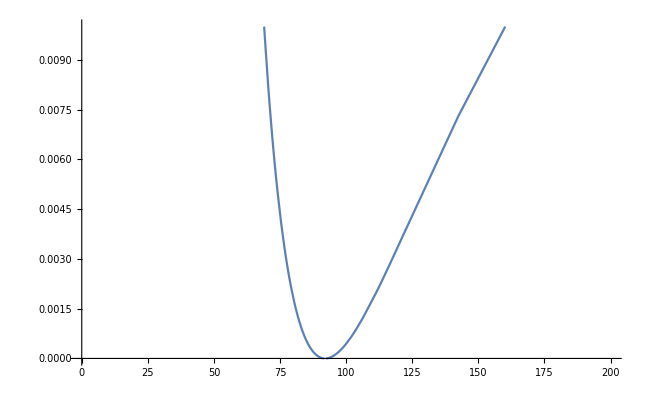

```mathematica
Block[{MH=125,Mt=172.50,Mb=4.250,Mc=1.230,Mτ=1.777,MW=80.385,GF=1.2057*10^-5,NC=3,α=1/137,λL=0.1,vv=242.17,MV1=100,g=0.6,e=0.3134},
Plot[Re[AnchoHAAN[XFt[4*Mt^2/MH^2],XFb[4*Mb^2/MH^2],XFc[4*Mc^2/MH^2],XFτ[4*Mτ^2/MH^2],XW[4*MW^2/MH^2],AO[MVC],BO[MH,MVC,MVC]]]/FDWHSM,{MVC,0,1000},PlotRange->{{0,200},{10^-6,0.01}}]]
```

```mathematica
Install["/home/bastilo/Documents/Programas/LoopTools-2.15/x86_64-Linux/bin/LoopTools"]
```

PaVe::shdw: Symbol PaVe appears in multiple contexts {LoopTools`,HighEnergyPhysics`fcloops`PaVe`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

Li2::shdw: Symbol Li2 appears in multiple contexts {LoopTools`,HighEnergyPhysics`FeynCalc`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

A0::shdw: Symbol A0 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`A0`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

B0::shdw: Symbol B0 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`B0`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

B1::shdw: Symbol B1 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`B1`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

B00::shdw: Symbol B00 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`B00`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

B11::shdw: Symbol B11 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`B11`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

DB0::shdw: Symbol DB0 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`DB0`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

DB1::shdw: Symbol DB1 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`DB1`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

C0::shdw: Symbol C0 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`C0`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

D0::shdw: Symbol D0 appears in multiple contexts {LoopTools`,HighEnergyPhysics`fctables`D0`}; definitions in context LoopTools` may shadow or be shadowed by other definitions.

====================================================
   FF 2.0, a package to evaluate one-loop integrals
 written by G. J. van Oldenborgh, NIKHEF-H, Amsterdam
 ====================================================
 for the algorithms used see preprint NIKHEF-H 89/17,
 'New Algorithms for One-loop Integrals', by G.J. van
 Oldenborgh and J.A.M. Vermaseren, published in 
 Zeitschrift fuer Physik C46(1990)425.
 ====================================================

LinkObject[…]

```mathematica
80.385/91.187
```

0.88154

```mathematica
√(1-0.881^2)
```

0.473116

```mathematica
(2*80.385*0.473)/0.313
```

242.953

```mathematica
λ2[λL_,MV1_,MVC_]:=λL+2*((MV1^2-MVC^2)/vv^2)
```